```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*"])//TableForm
```

data\bla1.csv
data\einzel.csv
data\erstemessung.ods
data\frequenzdoppel.ods
data\hauen1.csv
data\placeholder.txt
data\pockel.ods
data\tem00b.txt
data\tem00.txt
data\tem03.2.bmp
data\tem032b.txt
data\tem032.txt
data\tem03.bmp
data\tem10.bmp
data\tem10b.txt
data\tem10.txt
data\tem20.bmp
data\tem20b.txt
data\tem20.txt
data\zweitemesseung.ods

```mathematica
ρ[r_,w_]:=(2 (r)^2)/w^2;
f[r_,w_,θ_,p_,l_]:=(ρ[r,w])^l*(LaguerreL[p,l,ρ[r,w]])^2(Cos[l*θ])^2 Exp[-ρ[r,w]];
```

```mathematica
Plot3D[f[(x^2+y^2)^0.5,5,ArcTan[y/x],2,1],{x,-10,10},{y,-10,10},Axes->False,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotPoints->40]
```

-Graphics3D-

```mathematica
her[x_,y_,theta_,p_,l_]:=(HermiteH[p,(x*Sin[theta]+y*Cos[theta])]Exp[-(x*Sin[theta]+y*Cos[theta])^2]*HermiteH[l,(x*Cos[theta]-Sin[theta]*y)]Exp[-(x*Cos[theta]-Sin[theta]*y)^2])^2;
```

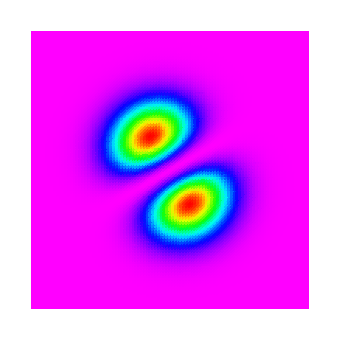
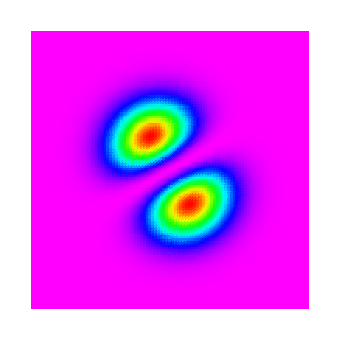

```mathematica
{DensityPlot[her[x,y,Pi/3,0,1],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,MaxRecursion->2,PlotPoints->100,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)],DensityPlot[f[(x^2+y^2)^0.5,1,ArcTan[y/x]+Pi/3,0,1],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,MaxRecursion->2,PlotPoints->100,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

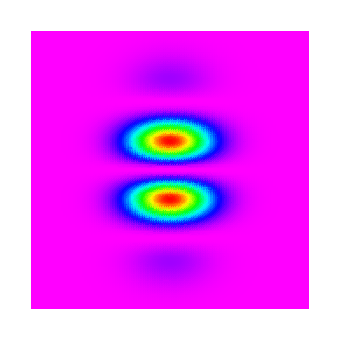
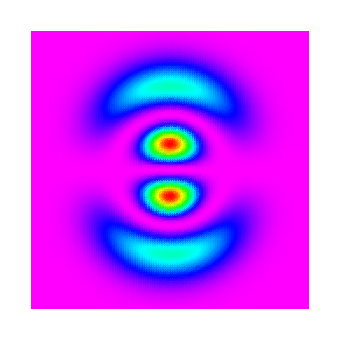
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(DensityPlot[her[x,y,Pi/2,0,#]+0her[x,y,Pi/2,0,0],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->120,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]&/@{3,5,7,9})~Join~{DensityPlot[f[(x^2+y^2)^0.5,1,ArcTan[y/x]-Pi/2,1,1],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->120,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

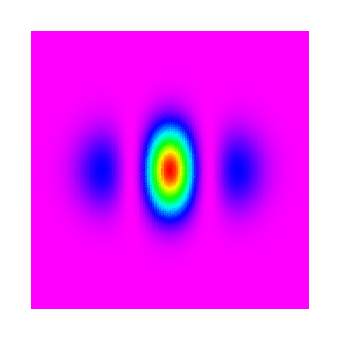
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(DensityPlot[her[x,y,Pi/2,#,0]+0her[x,y,Pi/2,0,0],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->120,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]&/@{2,4,6})~Join~{DensityPlot[f[(x^2+y^2)^0.5,1,ArcTan[y/x],1,0],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->120,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

```mathematica
{DensityPlot[her[x,y,Pi/2,2,0]+her[x,y,Pi/2,0,2],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,MaxRecursion->2,PlotPoints->120,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)],
DensityPlot[f[(x^2+y^2)^0.5,0.75,ArcTan[y/x],1,2],{x,-2.5,2.5},{y,-2.5,2.5},Frame->False,Axes->False,PlotRange->All,PlotPoints->120,ImageSize->340,ColorFunction->(Blend[{RGBColor[1,0,1],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[0,1,0],RGBColor[1,1,0],RGBColor[1,0,0]},#]&)]}
```

{-Graphics-,-Graphics-}

```mathematica
schnitt00=ReadList["data/tem00b.txt",Number];
schnitt10=ReadList["data/tem10b.txt",Number];
schnitt20=ReadList["data/tem20b.txt",Number];
schnitt30=ReadList["data/tem032b.txt",Number];
```

```mathematica
f00=Normal@NonlinearModelFit[schnitt00,a*her[(x-b)/c,0,0,0,0],{{a,200},{b,650},{c,100}},x]
Show[
ListPlot[schnitt00,PlotRange->All,PlotStyle->Gray],
Plot[f00,{x,0,1280},PlotRange->All,PlotStyle->Black],
Frame->True,Axes->None,FrameLabel->{"Pixel","Intensity (arb. units)"}
]
```

181.081 ⅇ^(-0.0000970795 (-664.11+x)^2)

-Graphics-

```mathematica
f10=Normal@NonlinearModelFit[schnitt10,a*her[(x-b)/c,0,0,0,1],{{a,200},{b,770},{c,200}},x,MaxIterations->1000]
Show[
ListPlot[schnitt10,PlotRange->All,PlotStyle->Gray],
Plot[f10,{x,0,1280},PlotRange->All,PlotStyle->Black],
Frame->True,Axes->None,FrameLabel->{"Pixel","Intensity (arb. units)"}
]
```

0.0448425 ⅇ^(-0.000101609 (-777.318+x)^2) (-777.318+x)^2

-Graphics-

```mathematica
f30=NonlinearModelFit[schnitt30,a*her[(x-b)/c,0,0,0,3],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f30=Normal@f30;
f50=Normal@NonlinearModelFit[schnitt30,a*her[(x-b)/c,0,0,0,5],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f70=Normal@NonlinearModelFit[schnitt30,a*her[(x-b)/c,0,0,0,7],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f90=Normal@NonlinearModelFit[schnitt30,a*her[(x-b)/c,0,0,0,9],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f110=Normal@NonlinearModelFit[schnitt30,a*her[(x-b)/c,0,0,0,11],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f130=NonlinearModelFit[schnitt30,a*her[(x-b)/c,0,0,0,13],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f130["RSquared"]
f130=Normal@f130;

Show[
ListPlot[schnitt30,PlotRange->All,PlotStyle->Gray],
Plot[{f30,f50,f70,f90,f110,f130},{x,0,1280},PlotRange->All,PlotStyle->Black],
Frame->True,Axes->None,FrameLabel->{"Pixel","Intensity (arb. units)"}
]
```

0.766801

-Graphics-

```mathematica
Show[
ListPlot[schnitt30,PlotRange->All,PlotStyle->Gray],
Plot[{Abs[NIntegrate[PDF[NormalDistribution[x,30],t]*1.2*10^(-14)*her[(t-815)/280,0,0,0,15],{t,x-100,x+100}]]},{x,0,1280},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Pixel","Intensity (arb. units)"}
]
```

-Graphics-

```mathematica
(*schnitt30p2=schnitt30;*)
ϕ[Δ_]:=Evaluate@PDF[NormalDistribution[0,32],Δ];
Dynamic[i]
Dynamic[n]
Dynamic[pos]
For[n=0,n<10,++n,
For[i=1,i≤Length[schnitt30],++i,
pos=Round@(Random[]*(Length@schnitt30-1)+1);
tmp=0;
diff=schnitt30⟦pos⟧-N@Sum[ϕ[pos-j]*schnitt30p2⟦j⟧,{j,Max[1,pos-40],Min[Length@schnitt30,pos+40]}];
For[j=Max[1,pos-40],j<=Min[Length@schnitt30,pos+40],++j,
schnitt30p2⟦j⟧=(schnitt30p2⟦j⟧+ϕ[pos-j]*diff)//N;
]
]
]
(*ListPlot[{schnitt30p2,schnitt30}]*)
```

```mathematica
Dynamic@Show[
ListPlot[{schnitt30p2,schnitt30},PlotRange->{{0,1280},{-10,150}},Frame->True,Axes->None,Joined->True],
Plot[0,{x,0,1280}]
]
```

```mathematica
schnitt30p3=schnitt30p2;
```

```mathematica
f30=NonlinearModelFit[schnitt30p2,a*her[(x-b)/c,0,0,0,3],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f30=Normal@f30;
f50=Normal@NonlinearModelFit[schnitt30p2,a*her[(x-b)/c,0,0,0,5],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f70=Normal@NonlinearModelFit[schnitt30p2,a*her[(x-b)/c,0,0,0,7],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f90=Normal@NonlinearModelFit[schnitt30p2,a*her[(x-b)/c,0,0,0,9],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f110=Normal@NonlinearModelFit[schnitt30p2,a*her[(x-b)/c,0,0,0,11],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f130=NonlinearModelFit[schnitt30p2,a*her[(x-b)/c,0,0,0,13],{{a,100},{b,800},{c,70}},x,MaxIterations->1000];
f130["RSquared"]
f130=Normal@f130;

Show[
ListPlot[schnitt30p2,PlotRange->All,PlotStyle->Gray,PlotRange->{0,160}],
Plot[{f30,f50,f70,f90,f110,f130},{x,0,1280},PlotRange->{0,160},PlotStyle->Black],
Frame->True,Axes->None,FrameLabel->{"Pixel","Intensity (arb. units)"},PlotRange->{-5,160}
]
```

0.813768

-Graphics-

```mathematica
schnitt10p2=schnitt10;
```

```mathematica
ϕ[Δ_]:=Evaluate@PDF[NormalDistribution[0,17],Δ];
Dynamic[i]
Dynamic[n]
Dynamic[pos]
For[n=0,n<10,++n,
For[i=1,i≤Length[schnitt10],++i,
pos=Round@(Random[]*(Length@schnitt10-1)+1);
tmp=0;
diff=schnitt10⟦pos⟧-N@Sum[ϕ[pos-j]*schnitt10p2⟦j⟧,{j,Max[1,pos-40],Min[Length@schnitt10,pos+40]}];
For[j=Max[1,pos-40],j<=Min[Length@schnitt10,pos+40],++j,
schnitt10p2⟦j⟧=(schnitt10p2⟦j⟧+ϕ[pos-j]*diff)//N;
]
]
]
(*ListPlot[{schnitt30p2,schnitt30}]*)
```

$Aborted

```mathematica
Dynamic@Show[
ListPlot[{schnitt10p2,schnitt10},PlotRange->{{0,1280},{-10,200}},Frame->True,Axes->None,Joined->True],
Plot[0,{x,0,1280}]
]
```

```mathematica
f10p2=Normal@NonlinearModelFit[schnitt10p2,(1-d*(x-740)^2)*a*her[(x-b)/c,0,0,0,1],{{a,200},{b,770},{c,200},{d,0}},x,MaxIterations->1000]
Show[
ListPlot[schnitt10p2,PlotRange->All,PlotStyle->Gray],
Plot[f10p2,{x,0,1280},PlotRange->All,PlotStyle->Black],
Frame->True,Axes->None,FrameLabel->{"Pixel","Intensity (arb. units)"}
]
```

0.0475548 ⅇ^(-0.000093698 (-779.259+x)^2) (1-7.64286×10^-6 (-740+x)^2) (-779.259+x)^2

-Graphics-